# Trap Calculations

New Notebook for CAL to calculate mangetic fields, magnetic field minima, and trap frequencies for initial and relaxed fields. All functions have been defined in the CAL_functions package.   

Contents: 
Constants & Functions
	Coil/Chip Info
	Functions
SM3 AI capable chip calculations
	Chip/System notes
	Magnetic Field Calc and Traps

Written by : Maren Mossman (MM) and Peter Engels (PE).  
Last Edited : 01.22.2021 (MM)

## Upload Constants & Functions

```mathematica
SetDirectory[NotebookDirectory[]] ;
Get["CAL_functions.m"]

(* For a list of functions/constants call *)
(*?"CALfunctions`*"*)
(* Make sure that you update the path to the CAL functions mathematica package! *)

FileNames["*","/Users/marenmossman/Desktop/NASA Project/mathematica/SM3"];
?"CALfunctions`*"
```

## Coil/Chip Info

#### Bias cage parameters

Changed the separation of the 
X-bias coils from 1.181 to 1.19105 (255 microns) 
Y-bias coils from 2.362 to 2.3572 (123 microns)
Z-bias coils from 3.228 to 3.10325 (3.169 mm) <-- Less believable
to match the measurements/calibrations from CQ.

```mathematica
(* 
In these lists, we have: 
 wiredia = coils[[1]];
	current = coils[[2]];
	width = coils[[3]];
	height = coils[[4]];
	coilspacing = coils[[5]];
	hmax = coils[[6]];
	rmax = coils[[7]]; 
	offset = coils[[8]];
*)

(*?"CALfunctions`YbiasCoils"
?"CALfunctions`ZbiasCoils"
?"CALfunctions`TransferCoils"
?"CALfunctions`MOTCoils"
?"CALfunctions`FFCoils"*)
```

#### SM3 Chip

```mathematica
(* 
When recording the chip design, you want to state the parameters for the entire coil. For the wires with 3 parts, you typically have a wire in the y-direction, the x-direction, and another y-direction. The order of these wires appear should be in the direction of source to sink, labeled in page 7 of CAL3A_chip&drivers_200128.pdf from JPL. The way in which the numbers are recorded is, e.g. a coil in the Y-direction: 
{x-fixed coordinate, y-start coordinate, y-end coordinate}
*)

(* 
Can only use 1 set of wires/coils per driver;
Driver 1: Z1, L2, T2;
Driver 2: Z2, L1, FF;
Driver 3: H-wires;
*)

(*?"CALfunctions`Za"
?"CALfunctions`Zb"
?"CALfunctions`La"
?"CALfunctions`Lb"
?"CALfunctions`Tb"
?"CALfunctions`Ha"
?"CALfunctions`Hb"*)
```

## Functions

### Magnetic Field Functions

General Notes

All B-field functions for square bias coils, chip, and breit-rabi corrections.

External Bias Fields

IMPORTANT: These parameters were found with the CAL schematics and spec sheets and should be fixed for each copy of the CAL apparatus with exception to the ϵ variable parameter.  Do Not Change the "*Coils[I_]" list functions in the CAL_functions package!

Below, find the coordinate transformation needed to accurately model the coils. Parameter ϵ, defined by default as 0, is used to take into consideration any offset of the atom chip (since it can vary for each different copy of the CAL system) - plan to use this parameter in real time to adjust system parameters.

Frequencies found for the external bias fields are harmonic enough that during calculations and the trajectory simulations, the acceleration is calculated using the frequencies because it is faster than using the real field.

External bias field coils can be run up to 8.0A, though for heating purposes, it may be best to not run them too high for too long.

The Transfer Coils and FF coils are the only ones that are centered at the atom chip.  The y-bias coils are centered 0.4525 in (11.5 mm) below the chip and the MOT coils are centered 0.591 in (15 mm) below the chip.  Therefore, if your y-bias field current is higher than your transfer current, you will start to pull the minimum away from the zero gradient of the field. Recommended to make use of the z-bias coils to recenter things to move the magnetic zero.

Each set of coils has a list consisting of: {wire diameter, current (variable), inner width, inner height, inner coil spacing, number of windings out, number of windings up, z-offset from the atom chip}. These lists can be found in the CAL_functions package.

Set up where coordinates are defined wrt atom chip coordinates (x, y, z):
- Transfer, MOT, and FF coils are oriented in the same direction (z’ = x, y’ = z, x’ = y). 
- The transfer coils and the FF coils are centered on the atom chip +/- ϵ.   
- The Y-bias coils are offset and rotated such that (z’’ = x’, y’’ = y’, x’’ = -z’). 
- The Z-bias coils are offset and rotated such that (z’’’ = y’, x’’’ = x’, y’’’ = -z’).

Magnetic field of a square wire loop

NOTES:
- All coils point with their axis into the z direction. 
- Each coil is a list consisting of the following elements found in "Coil Information": {width,height,x,y,z,current}. 
- Lengths are in meters,currents in Amps. 
- Width is in x direction, Height in y direction.

Note that this calculates the magnetic field of rectangular solenoids in Tesla.

z’ = x-direction on chip
x’ = y-direction on chip
y’ = z-direction from chip

Field Functions
Bz[], By[], Bx[], BxField[], ByField[], BzField[], BxSum[], BySum[], BzSum[], FieldMag[], BiasCoils[]

Coil Lists
YbiasCoils, ZbiasCoils, TransferCoils, MOTCoils, FFCoils

Atom Chip Fields

The field functions for the chip traces take Biot-Savart of a finite length of wire, either in the x-direction (Xwire) or the y-direction (Ywire).  The input for these two functions are the height away from the inner surface of the chip that is 100 microns thick and the coordinates of the wire (position and length). This code was developed by the team at JPL and sent to users for the CAL project.  It has since been modified by MM for changes to the flight system.

These functions have been updated to calculate the field in Tesla.

Field Functions
Xwire[], Ywire[], ChipTrapField[], ChipTrapFieldFAST[] (Use the FAST functions to use the constant magnetic fields)

### Magnetic Field Tests

Note : When running these tests, be sure to use "None" for the Trap Parameters. Otherwise, if you try to calculate the B - field at {0, 0, 0} (the chip center), you will return a slew of 1/0 errors.

```mathematica
{EnergyBR[2,2,31.05Gauss,"Rb87"]-EnergyBR[2,1,31.05Gauss,"Rb87"]}/hPlanck/MHz
{EnergyBR[2,1,31.05Gauss,"Rb87"]-EnergyBR[2,0,31.05Gauss,"Rb87"]}/hPlanck/MHz
{(EnergyBR[2,2,31.05Gauss,"Rb87"]-EnergyBR[2,1,31.05Gauss,"Rb87"])-(EnergyBR[2,1,31.05Gauss,"Rb87"]-EnergyBR[2,0,31.05Gauss,"Rb87"])}/hPlanck/MHz
```

{21.5153}

{21.6513}

{-0.13599}

Currents list={iD1, iD2, iD3, iT, iM, iY, iZ, iFF}; magnetic field calibrations: Xbias=40.625G, Ybias=14.286G, Zbias=10.3675G

```mathematica
Reference={0,0,0,0.22,0,-2.567,0.150,0};
TrapParams={"Rb87",2,2,"None","None","None"};
(*(ChipTrapField[0,0,0,Reference,TrapParams]/Gauss);*)
XbiasGperA=(ChipTrapField[0,0,0,{0,0,0,1,0,0,0,0},TrapParams]/Gauss)
MOTGperA=(ChipTrapField[0,0,0,{0,0,0,0,1,0,0,0},TrapParams]/Gauss)
YbiasGperA=(ChipTrapField[0,0,0,{0,0,0,0,0,1,0,0},TrapParams]/Gauss)
ZbiasGperA= (ChipTrapField[0,0,0,{0,0,0,0,0,0,1,0},TrapParams]/Gauss)
FFGperA =(ChipTrapField[0,0,0,{0,0,0,0,0,0,0,1},TrapParams]/Gauss)
(*((MagTrapField[0,0,0.101mm,{0,0,0,1,0,0,0,0},TrapParams]-MagTrapField[0,0,0.001mm,{0,0,0,1,0,0,0,0},TrapParams])/(0.1mm))*100*)
```

42.1503

19.9513

14.1323

9.80735

0.617795

```mathematica
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,x,0,0,0},TrapParams]/Gauss},{x,0,3,0.25}],PlotRange->{-0.1,3.75},Frame-> True,GridLines-> {{0.5,1,1.5,2,2.5,3}, {0.5,1,1.5,2,2.5,3,3.5}},FrameLabel-> {"Current [A]","B [Gauss]"},PlotStyle->Yellow,PlotMarkers->{Automatic,12},Joined->True]
```

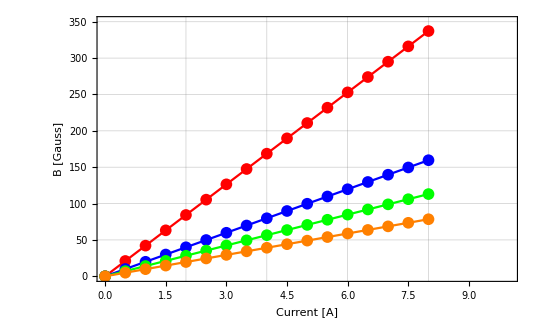

```mathematica
Show[
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,x,0,0,0,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotRange->{{0,10},{0,350}},Frame-> True,GridLines-> {{2,4,6,8}, {50,100,150,200,250,300,350}},FrameLabel-> {"Current [A]","B [Gauss]"},PlotStyle->Red,PlotMarkers->{Automatic,12},Joined->True],
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,0,x,0,0,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotStyle->Blue,PlotMarkers->{Automatic,12},Joined->True],
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,0,0,x,0,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotStyle->Green,PlotMarkers->{Automatic,12},Joined->True],
ListPlot[Table[{x,ChipTrapField[0,0,0,{0,0,0,0,0,0,x,0},TrapParams]/Gauss},{x,0,8.0,0.5}],PlotStyle->Orange,PlotMarkers->{Automatic,12},Joined->True]
]
```

## SM3 AI capable chip calculations

## Chip/System Notes (SM3 AI capable chip)

Note: 
- Chosen coordinate system: "x" is the direction of the main chip wire, and "y" is the direction current flows along the cross wire. Coordinates of the wire are defined from left to right on the image Dave sent (ambient side) (i.e. Example = {{left y wire coord}, {main x wire coord}, {right y wire coord}}). 
- Z wires are current limited to 3.5 A (Z1 - 1.0 A flight, Z2 - 2.75 A flight)
- H wires are current limited to 5.0 A (H wires - 2.75 A flight)

MOT and Transfer coils can handle up to 8.0 A, while the Y and Z wires can run up to 3.0 A.

Fast Feshbach (FF) coils are now run by current driver 2, which means that they cannot be running at the same time as Z2 and L1.

Note: For the relationship between the CAL table system and the current that goes into the wires:

X-bias coils: 0.081 A == 10 mV

Y-bias coils: 0.029 A == 10 mV

Z-bias coils: 0.030 A == 10 mV

Z1 (L) chip: 0.85 A == 0.243 V

Z2 (Z) chip: 2.4 A == -0.686 V

H wires chip: 2.3 A == 0.46 V

-Graphics-

## Magnetic Field Calculations and Traps

### Notes

In this section, we define functions to calculate features of the magnetic traps with the atom chip and the megnetic fields for the Feshbach resonances. All but the ChipTrapField functions can be found in the CALfunctions` package, due to changes in which traces you want to use.

Note: Members of the team at JPL have said they use L2, Z2, and the H-wires to generate a BEC, so we use these as a test set.

Field Functions
ChipTrapField[] - Use for precise calculations SM3 AI chip (uses real fields)
ChipTrapFieldFAST[] - Use for fast calculations SM3 AI chip (uses approximate fields)

### Trap Parameters

#### Set your currents here

Make a list of 8 currents in the following order: 

{I_driver1, I_driver2, I_driver3, I_transfercoils, I_MOTcoils, I_ybiascoils, I_zbiascoils, I_FFcoils} ***

*** For reference: Dave Aveline (JPL) says that with SM3 AI chip, {0.85,2.40,2.30,-0.222,0,2.545,-0.160,0}*A, they get a BEC with Rb-87 in gravity at the GTB.

```mathematica
(* Confirmed traps with the flight apparatus, current provided by Dave Aveline on April 24, 2019. *)
iLb=0.851;
iZb =2.401;
iH = 2.300;
iTx = -0.220;
iYy = 2.567;
iZz =-0.150;
currents = {iLb,iZb,iH,iTx,0,iYy,iZz,0}*A;
```

#### State how you are preparing your atoms in (initial trap)

Note : All atoms are prepared in the | 2, 2 > state on CAL for both Rb and K. All minimizing functions and trap frequencies are found using the Breit - Rabi energy calculation, so specifying the F and mF states in your trap parameters is very important for calculating the trap frequencies. For microgravity, set g = 0. D1, D2, D3 are the drivers 1, 2, and 3, respectively.

```mathematica
grav=0;
yguess = -1.0mm;
F=2;
mF=2;
isotope="Rb87";
D1="L2";
D2="Z2";
D3 = "H";
TrapParams = {isotope,F,mF,D1,D2,D3}
```

{Rb87,2,2,L2,Z2,H}

#### Test whether or not the trap parameters you entered above are valid!

If your trap parameters are invalid, the test function will return with an error function.

```mathematica
Btest = ChipTrapFieldFAST[0,yguess,0.2mm,currents,TrapParams]
Btest2 = ChipTrapField[0,yguess,0.2mm,currents,TrapParams]
```

0.00156931

0.00153869

#### Calculate minima, magnetic fields and frequencies using FAST functions

```mathematica
{xi,yi,zi}=zminFAST[currents,TrapParams,grav,yguess]
Bmin = ChipTrapFieldFAST[xi,yi,zi,currents,TrapParams]/Gauss
Trapbottom ={EnergyBR[2,2,Bmin*Gauss,"Rb87"]-EnergyBR[2,1,Bmin*Gauss,"Rb87"]}/hPlanck/MHz
Freq =  ChipTrapFreqFAST[xi,yi,zi,currents,TrapParams,0]
```

{0.0004349979395,-0.001011688738,0.0001493763978}

11.2893

{7.87033}

{31.9366,735.023,756.544}

#### Calculate minima, magnetic fields and frequencies using full fields (WARNING: VERY SLOW - takes about a minute to run)

```mathematica
{xi,yi,zi}=zmin[currents,TrapParams,grav,yguess]
Bmin = ChipTrapField[xi,yi,zi,currents,TrapParams]/Gauss
Trapbottom ={EnergyBR[2,2,Bmin*Gauss,"Rb87"]-EnergyBR[2,1,Bmin*Gauss,"Rb87"]}/hPlanck/MHz
Freq =  ChipTrapFreq[xi,yi,zi,currents,TrapParams,0]
```

{-0.00002262488042,-0.001000359471,0.0001332562387}

#### Check Mag Fields

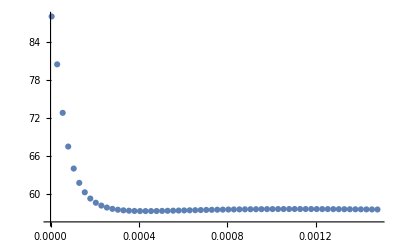

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[xi,yi,z,currents,TrapParams]/Gauss},{z,0.005mm,1.5mm,0.025mm}],PlotRange->All]
```

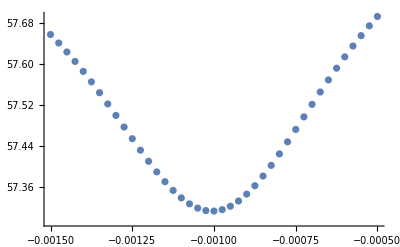

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[xi,z,zi,currents,TrapParams]/Gauss},{z,-1.5mm,-0.5mm,0.025mm}],PlotRange->All]
```

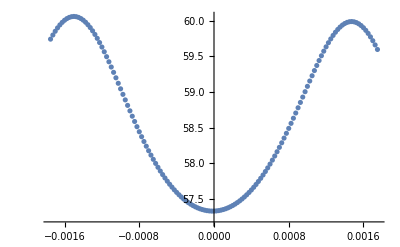

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[z,yi,zi,currents,TrapParams]/Gauss},{z,-1.75mm,+1.75mm,0.025mm}],PlotRange->All]
```

```mathematica
ListPointPlot3D[Table[1000*PE[xi,y*mm,z*mm,currents,TrapParams,0],{z,0.05,1,0.05},{y,-1.5,-0.5,0.05}],PlotRange->All]
```

-Graphics3D-

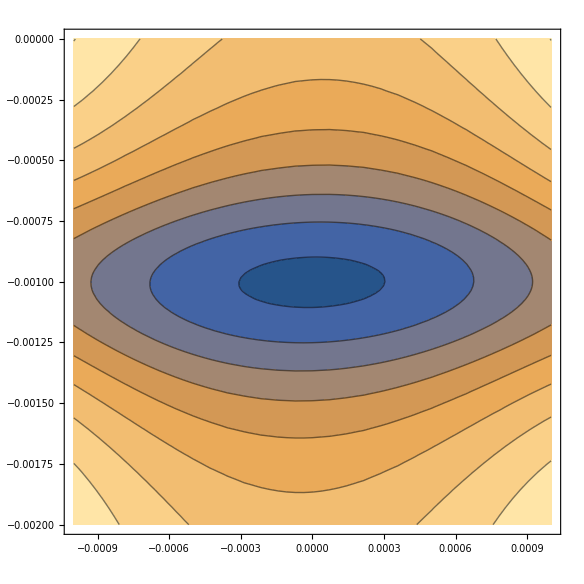

```mathematica
ContourPlot[ChipTrapFieldFAST[x,y,zi,currents,TrapParams]/Gauss,{x,-1mm,1mm},{y,-2mm,0mm}]
```

#### Ramp Sequencing from initial trap to final trap

Initial Trap : {0.85, 2.4, 2.3, -0.222, 0, 2.55, -0.15, 0}
Final IP Trap : {0., 3.2, 1., -0.729, 0, 0.765, 0., 0}

```mathematica
(*Change in each current parameter*)
ΔL = 0.85-0;
ΔZ = 2.4 - 3.2;
ΔH = 2.3 - 1.0;
ΔX = -0.222-(-0.729);
ΔY = 2.55 - 0.765;
Δz = -0.15 - 0;
```

```mathematica
(*Create a list of the current values to double check that the iterations work*)
For[i=0,i<10,i++,
frac = 1-(i*0.1);Print[{0.85-(ΔL*frac),2.4-(ΔZ*frac),2.3-(ΔH*frac),-0.222-(ΔX*frac),0,2.55-(ΔY*frac),-0.15-(Δz*frac),0}]]
```

```mathematica
Clear[zlist]
```

```mathematica
(* Prints minimum values, magnetic min, and frequencies to check for discontinuities*)
TrapParams = {isotope,F,mF,D1,D2,D3};

For[i=0,i<21,i++,
frac =1-(i*0.05);
currents={0.85-(ΔL*frac),2.4-(ΔZ*frac),2.3-(ΔH*frac),-0.222-(ΔX*frac),0,2.55-(ΔY*frac),-0.15-(Δz*frac),0}*A;
{xi,yi,zi}= zminFAST[currents,TrapParams,0];
Bmin = ChipTrapFieldFAST[xi,yi,zi,currents,TrapParams]/Gauss;
Freq =  ChipTrapFreqFAST[xi,yi,zi,currents,TrapParams,0];
Print[{currents, {xi,yi,zi},Bmin, Freq} ]]
```

```mathematica
zlist
```

#### Ramping Magnetic field instead of RF frequency

Want to ramp the B field instead of the frequency of the RF, due to issues with the frequency at which we are able to do the RF ramps. Need to figure out if we have the RF frequency sitting at a particular value, what magnetic field values for the x-bias field are needed to do the ARP from the |2,2> state into the |2,1> state. 

Lets say that the code is perfect and our IP trap bottom is 31.16 G. Assuming the BR formula is giving the correct shift in the energy levels, this should lead to a state energy separation of 21.5908 MHz between the |2,2> and the |2,1> states. For the same magnetic field bottom, this yeilds a state separation of 21.7278 MHz between the |2,1> and the |2,0> states. This is a difference of 136.946 kHz. Now, if we sit at the resonant frequency for this trap bottom (21.5908 MHz), but then vary the trap bottom using the x-bias coils, what is the precision in the current that we would need to be successful in populating the |2,1> state but not the |2,0> state?

```mathematica
(*RF21[B_,iso_]:=(EnergyBR[2,2,B*Gauss,iso]-EnergyBR[2,1,B*Gauss,iso])/hPlanck/MHz;
RF10[B_,iso_]:=(EnergyBR[2,1,B*Gauss,iso]-EnergyBR[2,0,B*Gauss,iso])/hPlanck/MHz;*)
(*{RF21[58,TrapParams[[1]]],RF10[58,TrapParams[[1]]]}
{RF21[58,TrapParams[[1]]]-RF10[58,TrapParams[[1]]]}*)
(*(RF10[31.16,"Rb87"]-RF21[31.16,"Rb87"])*1000*)
```

```mathematica
currents = {3.2,-0.399*0,0,0.2645*2.685,0,2.55*0.3,0.2100*0,0}(* This is the IP TRAP!!! *)
currents = {3.2,-0.399*0,0,0.2645*2.715,0,2.55*0.3,0.2100*0,0}(* This is the IP TRAP!!! *)
TrapParams = {"Rb87",2,2,"Orange","Orange","None"};

{xi,yi,zi} = zminFAST[currents,TrapParams,0]
Bmin = ChipTrapFieldFAST[xi,yi,zi,currents,TrapParams]/Gauss

{RF21[Bmin,TrapParams[[1]]]-21.5904,RF10[Bmin,TrapParams[[1]]]-21.5904}
```

```mathematica
{3.2*(0.914/3.2),-0.399*(0.914/3.2),0,0.2645*(-0.0319/0.2645),0,2.55*(0.83/2.55),0.2100*(-0.07/0.2100),0}
{3.2*(0.914/3.2),0*-0.399*(0.914/3.2),0,2.7*0.2645*(-0.0319/0.2645),0A,0.3*2.55*(0.83/2.55),0*0.2100*(-0.07/0.2100),0A}
```

{0.914,-0.113964,0,-0.0319,0,0.83,-0.07,0}

{0.914,0.,0,-0.08613,0,0.249,0.,0}

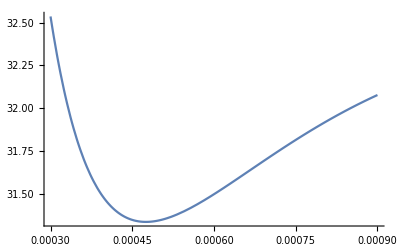

```mathematica
Plot[ChipTrapFieldFAST[0,0,z,currents,TrapParams]/Gauss,{z,0.300mm,0.900mm}]
```

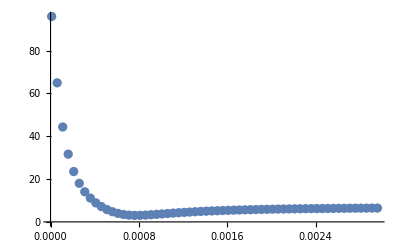

```mathematica
ListPlot[Table[{z,ChipTrapFieldFAST[0,0,z,{3.5,0,0,0,0,7/14.286,0,0},TrapParams]/Gauss},{z,0.01mm,3mm,0.05mm}],PlotRange->All]
```

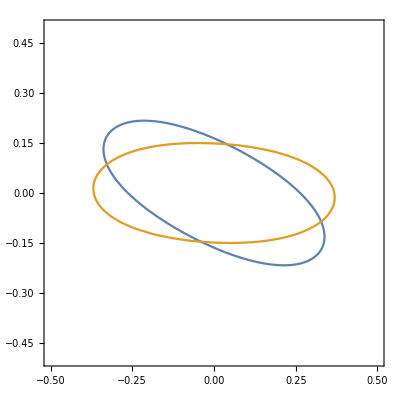

```mathematica
(*f[{x_,y_}]:=ChipTrapFieldFAST[x mm,y mm,zi,currents,TrapParams]/Gauss;
ContourPlot[{f[{x,y}]==31.5,f[RotationTransform[-24Degree,{xi,yi}][{x,y}]]==31.5},{x,-0.5,0.5},{y,-0.5,0.5}]*)
```

```mathematica
(*TrapParams = {isotope,F,mF,D1,D2,D3};
zlist = {};
For[i=0,i<10,i++,
factor = 1-(i*0.1);
currents={0.4,-1.2,0,factor*0.4,0,factor*0.7,0,0}*A;
(*currents ={0.4428A,0.00,0,i/14*0.7627,0A,0.4675,0A,0A};*)
{xi,yi,zi}= zmin[currents,TrapParams,0];
zlist = Append[zlist,zi];]
(*For[i=1,i<8,i++,
factor=1-(i*0.1);
currents={0.4,-1.2,0,factor*0.04,0,0.07,0,0}*A;
{xi,yi,zi}= zmin[currents,TrapParams,0];
zlist = Append[zlist,zi];]*)
*)
```

```mathematica
(*RampPics={};
For[i=0,i<10,i++,
factor = 1-(i*0.1);
currents={0.4,-1.2,0,factor*0.4,0,factor*0.7,0,0}*A;
AdiaRamp = ContourPlot[ChipTrapFieldFAST[x mm,y mm,zlist[[i+1]],currents,TrapParams]/Gauss,{x,-1,1},{y,-1,1},Contours->20];
RampPics=AppendTo[RampPics,AdiaRamp];]
For[i=0,i<8,i++,
factor = 1-(i*0.1);
currents={0.4,-1.2,0,factor*0.04,0,0.07,0,0}*A;
AdiaRamp = ContourPlot[ChipTrapFieldFAST[x mm,y mm,zlist[[i+11]],currents,TrapParams]/Gauss,{x,-1,1},{y,-1,1},Contours->20];
RampPics=AppendTo[RampPics,AdiaRamp];]*)
```

```mathematica
(*Export["SecondEfimovRamp.gif",RampPics,"DisplayDurations"-> 1];*)
```

#### Attempting to Optimize...

```mathematica
(*list = {{0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0}, {1, 1, 1, 0, 0, 0}, {1, 1, 1, 1, 0, 0}, {1, 1, 1, 1, 1, 0}, {1, 1, 1, 1, 1, 1}};
list1 = Permutations[list[[1]]];
list2 = Permutations[list[[2]]];
list3 = Permutations[list[[3]]];
list4 = Permutations[list[[4]]];
list5 = Permutations[list[[5]]];
list6 = Permutations[list[[6]]];
list7 = Permutations[list[[7]]];
listTOT =  Join[list1, list2, list3, list4, list5, list6, list7];*)
```

```mathematica
(*BestFitFunct[id1_, id2_, iT_, iM_, iY_, iZ_] := Module[{factor, xi, yi, zi, Bmin, result},
  result = ConstantArray[0, {64, 2}];
  For[i = 1, i < 3, i++,
    factor = (-1)^listTOT[[i]];
    id1 = id1*factor[[1]];
    id2 = id2*factor[[2]];
    iT = iT*factor[[3]];
    iM = iM*factor[[4]];
    iY = iY*factor[[5]];
    iZ = iZ*factor[[6]];
    {xi, yi, zi} = zminTRAP[id1, id2, iT, iM, iY, iZ, 0, 1];
    xi = xi[[2]];
    yi = yi[[2]];
    zi = zi[[2]];
    Bmin = ChipTrapField[xi, yi, zi, id1, id2, iT, iM, iY, iZ, 0];
    result[[i]][[1]] = factor;
    result[[i]][[2]] = Bmin;
    ]
   Return[result]
  ]
*)
```

```mathematica
(*For[i = 1, i < 65, i++,
 factor = (-1)^listTOT[[i]];
 {xi, yi, zi} = zminTRAP[factor[[1]]*iD1, factor[[2]]*iD2, factor[[3]]*iTtrap, factor[[4]]*iMtrap, factor[[5]]*iYtrap, factor[[6]]*iZtrap, iFFtrap, 1];
 xi = xi[[2]];
 yi = yi[[2]];
 zi = zi[[2]];
 Bmin = ChipTrapField[xi, yi, zi, factor[[1]]*iD1, factor[[2]]*iD2, factor[[3]]*iTtrap, factor[[4]]*iMtrap, factor[[5]]*iYtrap, factor[[6]]*iZtrap, iFFtrap];
 Print[{{factor}, {xi, yi, zi}, Bmin}]
 ]*)
```